# 机器学习简介

```mathematica
-Graphics-        -Graphics-
```

## 大纲

机器学习

什么是机器学习 - What Is Machine Learning ？

典型任务 - Typical Tasks

学习范式 - Learning Paradigms

监督学习 - Supervised Learning

无监督学习 - Unsupervised Learning

强化学习 - Reinforcement Learning

相关领域：数据挖掘 - Related Field: Data Mining

Wolfram 语言中的机器学习 - Machine Learning in the Wolfram Language

自动机器学习框架 - Automatic Machine Learning Framework

神经网络框架 - Neural Networks Framework

使用机器学习实现的功能 - Functions Implemented Using Machine Learning

内置机器学习 - Built-in Machine Learning

内置分类器 - Built-in Classifiers

ImageIdentify, ImageCases

AudioIdentify

TextStructure

FindTextualAnswer

TextCases

预训练网络 (NetModel) - Pre-trained Networks (NetModel)

监督学习 - Supervised Learning

Classify

Predict

[A] 文本分类 - Text Classification

[A] 图像分类 - Image Classification

[A] 数据预测 - Data Prediction

监督方法 - Supervised Methods

线性回归 - Linear Regression

逻辑回归 - Logistic Regression

最近邻方法 - Nearest Neighbors

决策树、随机森林、梯度提升树 - Decision Trees, Random Forest, Gradient-Boosted Trees

支持向量机 - Support Vector Machine

高斯过程 - Gaussian Processes

[P] 分类 - Classification

聚类 - Clustering

基本聚类 - Basic Clustering

聚类分类 - ClusterClassify

[A] 点聚类 - Point Clusters

[A] 图像聚类 - Image Clusters

[A] 色聚类 - Color Clusters

聚类方法 - Clustering Methods

KMeans

SpanningTree

DBSCAN

玩具示例 - Toy Examples

[P] 聚类 - Clustering

维度聚类 - Dimensionality Clustering

点 - Points

图像 - Images

[A] 缺失数据插补 - Missing Data Imputation

LearnDistribution

分类空间 - Categorical Space

数值空间 - Numeric Space

结构化数据 - Structured Data

[P] LearnDistrubution

LearnDistribution 方法 - LearnDistribution Methods

Multinormal

GausianMixture

KernelDensityEstimation

ContingencyTable

FindDistribution 与 FindFormula

FindDistribution

FindFormula

良好实践 - Good Practices

如何训练模型？- How to Train a Model?

优化实验 - Optimization Experiment

了解有关机器学习的更多信息... - To Know More About Machine Learning...

资源 - Resources

教育 - Education

## 机器学习 - Machine Learning

### 什么是机器学习？ - What Is Machine Learning?

不给出明确指令的编程 - Programming without giving explicit instruction

通常，计算机从数据中”学习”模型 - Typically, a computer “learns” a model from data

模型 = 带有可调参数的程序 - model = program with tunable parameters

学习 = 调整参数以适应数据 - learning = tuning parameters to fit data

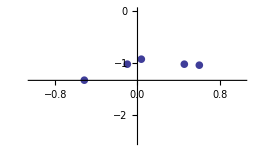
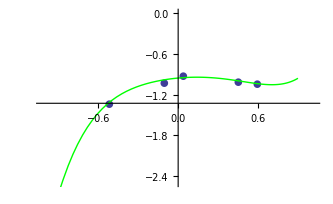
-Graphics-	⟶	-Graphics-

{ →cat, →dog,...}	⟶	-Graphics-

### 典型任务 - Typical Tasks

图像、声音、文本等的分类 - Classification of images, sound, text, etc.

→cat, →dog,...

数据集中变量的预测 - Prediction of a variable in a dataset

(6 yo, female) → 1.15 m, (11 yo, male) → 1.48 m, …

文本翻译 - Text translation

“the house is blue” → “la maison est bleue”

时间序列的预测 - Prediction of a time series

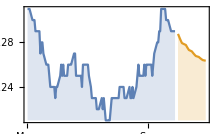

异常检测 - Anomaly detection

-Graphics-

数据聚类 - Data clustering

-Graphics-

机器人学习如何走路 - Robot learning how to walk

-Graphics-

玩游戏 - Playing games

## 学习范式 - Learning Paradigms

### 监督学习 - Supervised Learning

来自示例的输入→输出映射 - Input → output mapping from examples

最常见的范式 - Most common paradigm

Wolfram 语言函数： - Wolfram Language functions:

Classify

Predict

### 无监督学习 - Unsupervised Learning

只有未标记的数据 - Only unlabeled data

（关注度在增加中） - (On the rise)

更多样化的任务集 - More diverse set of tasks

Wolfram 语言函数：- Wolfram Language functions:

ClusterClassify, FindClusters

DimensionReduction, FeatureExtraction

SequencePredict

LearnDistribution

AnomalyDetection

SynthesizeMissingValues

### 强化学习 - Reinforcement Learning

智能代理采取行动，来自环境的反馈 - An intelligent agent takes actions, feedback from an environment

目标是最大化奖励 - The goal is to maximize a reward

还没有太多使用（但有很多研究） - Not much used yet (but lot of research)

Wolfram 语言函数： - Wolfram Language functions:

BayesianMinimization

ActiveClassification, ActivePrediction

Train an Agent in a Reinforcement Learning Environment
Reinforcement Learning with System Modeler

其他任务 - Other tasks

学习方针 - Learning policy

### 相关领域：数据挖掘 - Related Field: Data Mining

提取或发现大型数据集中的模式 - Extract or discover patterns in large datasets

Wolfram 语言函数：- Wolfram Language functions:

FindFormula

FindDistribution

## Wolfram 语言中的机器学习

### 自动机器学习框架 - Automatic Machine Learning Framework

函数 - Functions

Classify & Predict

ClusterClassify, FindClusters

DimensionReduction, FeatureExtraction

…

任务导向 - Task oriented

分类 - classification

预测 - prediction

聚类 - clustering

维数简化 - dimensionality reduction

…

全自动 - Fully automated

数据预处理 - data preprocessing

方法选择 - method selection

超参数选择 - hyperparameter selection

### 神经网络框架 - Neural Networks Framework

单一方法框架 - Single-method framework

面向模型 - Model oriented

高灵活性 - High flexibility

模块工具箱 - modular toolbox

高性能 - High performance

### 使用机器学习实现的函数 - Functions Implemented Using Machine Learning

预训练网络 (NetModel) - Pre-trained network (NetModel)

内置分类器 [指南] - Built-in classifiers [guide]

ImageIdentify, TextCases, FindImageText, FacialFeatures, etc.

## 内置机器学习 - Built-in Machine Learning

### 内置分类器 - Built-in Classifiers

预训练，立即可用 - Pre-trained, immediately usable

```mathematica
Classify["Language","What is this"]
```

English

```mathematica
Classify["Language","C'est quoi?"]
```

French

可作为普通 ClassifierFunction 表达式使用 - Available as normal ClassifierFunction expressions

```mathematica
Classify["FacebookTopic"]
```

ClassifierFunction[…]

```mathematica
%["I play football"]
```

Sports

易于嵌入其他代码 - Easy to embed in other code

```mathematica
DynamicModule[{x=""},
Column[{
InputField[Dynamic[x], String, ContinuousAction->True],
Dynamic[Column@Classify["FacebookTopic",x,"TopProbabilities"->3]]
}]]
```

### ImageIdentify, ImageCases

图像识别和物体检测 - Image recognition and object detection

```mathematica
ImageContents[-Graphics-]
```

图像识别和物体检测 - Image recognition and object detection

```mathematica
ImageCases[-Graphics-,Entity["Concept","CanisFamiliaris::597qc"]->EntityProperty["Concept","EquivalentEntity"]]
```

{dog}

```mathematica
EntityValue[%,{EntityProperty["Species","ScientificName"],EntityProperty["Species","BodyTemperature"]}]
```

{{Canis lupus familiaris,(99.4to104.) °F}}

可用于构建基于神经网络的应用程序 - Can be used to build neural network-based applications

```mathematica
imageCaption[i_Image] := With[{detections=Length/@ImageCases[i,AcceptanceThreshold->0.5]},If[Length[detections]==0,"An image with no identified objects.",("An image with "<>Riffle[Riffle[KeyValueMap[StringRiffle[{IntegerName[#2],Pluralize[#1["Name"],#2]}]&,detections],", ",{2,-3,2}]," and ",{-2,-2,1}])<>"."]]
```

```mathematica
imageCaption[-Graphics-]
```

An image with one dining table, three bowls, one cup and one spoon.

### AudioIdentify

识别录音中的主要声音 - Identify the the main sounds in an audio recording

```mathematica
AudioIdentify[]
```

chirp

后端在 Wolfram 神经网络储存库 中可公开使用 - The backend is publicly available in the Wolfram Neural Net Repository

```mathematica
net=NetModel["Wolfram AudioIdentify V1 Trained on AudioSet Data"]
```

NetChain[<>]

### TextStructure

找出文本的语法结构 - Find the grammatical structure of text

```mathematica
TextStructure["The cat is on the mat."]
```

The
Determinercat
Noun
Noun Phrase  is
Verb  on
Preposition  the
Determinermat
Noun
Noun Phrase
Prepositional Phrase
Verb Phrase.
Punctuation
Sentence

### FindTextualAnswer

尝试在给定的文本中找到问题的答案 - Attempts to find the answer to a question in a given piece of text

http://blog.wolfram.com/2018/02/15/new-in-the-wolfram-language-findtextualanswer

```mathematica
FindTextualAnswer["The dodo (Raphus cucullatus) is an extinct flightless bird that was endemic to the island of Mauritius, east of Madagascar in the Indian Ocean. The dodo's closest genetic relative was the also extinct Rodrigues solitaire, the two forming the subfamily Raphinae of the family of pigeons and doves. The closest living relative of the dodo is the Nicobar pigeon. A white dodo was once thought to have existed on the nearby island of Réunion, but this is now thought to have been confusion based on the Réunion ibis and paintings of white dodos.\n
Subfossil remains show the dodo was about 1 metre (3 ft 3 in) tall and may have weighed 10.6–17.5 kg (23–39 lb) in the wild. The dodo's appearance in life is evidenced only by drawings, paintings, and written accounts from the 17th century.",
"How big was the dodo?"]
```

1 metre

在 神经网络存储库 中的后端可公开使用 - The backend is publicly available in the Neural Net Repository

```mathematica
NetModel["Wolfram FindTextualAnswer Net for WL 11.3"]
```

NetGraph[<>]

### TextCases

在一段文本中执行自动实体标记 - Perform automatic entity tagging in a piece of text

```mathematica
TextContents["The flag of Italy is green, white and red. Since 1861, the capital is Rome, which also serves as the capital of the Lazio region. With 2,872,800 residents in 1,285 km2 (496.1 sq mi)"]
```

可用于从文本数据中提取语义信息 - Can be used to extract semantic information from textual data

```mathematica
TextCases[StringTake[WikipediaData["Planets"],10000],"Planet"]//Tally
```

{{terrestrial planets Mercury,1},{Venus,10},{Earth,19},{Mars,6},{Jupiter,6},{Saturn,6},{Uranus,3},{Neptune,3},{Mercury,5},{Jupiters,1},{Earths,1}}

在 神经网络存储库 中的后端模型可公开使用 - The backend models are publicly available in the Neural Net Repository

词嵌入 - word embedding

```mathematica
NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"]
```

NetGraph[<>]

分类 - classification

```mathematica
NetModel["Wolfram Entity Recognition Net for TextCases WL 12.0 V2"]
```

NetGraph[<>]

### 预训练网络 (NetModel) - Pre-trained Networks (NetModel)

https://resources.wolframcloud.com/NeuralNetRepository

使用它们构建更多应用程序 - Use them to build more applications

示例：使用 GPT 2 生成文本 - Example: text generation with GPT 2

```mathematica
lm=NetModel[{"GPT2 Transformer Trained on WebText Data","Task"->"LanguageModeling"}];
generateSample[languagemodel_][input_String,numTokens_:10,temperature_:1]:=Nest[Function[StringJoin[#,languagemodel[#,{"RandomSample","Temperature"->temperature}]]],input,numTokens];
```

```mathematica
generateSample[lm]["Albert Einstein was",20]
```

Albert Einstein was transmuted into a big human stepchild of 1736. Besides most people obviously making use of the

## 监督学习 - Supervised Learning

监督学习函数 - Supervised learning functions

来自范例的输入 → 输出映射 - Input → output mapping from examples

最经典的任务 - Most classic tasks

分类：输出 = 离散类 - Classification: output = discrete classes

回归：输出 = 连续数字 - Regression: output = continuous numbers

### 分类 - Classify

给定输入中的一个或多个特征，预测最可能的示例类 - Given one or more features in input, predict the most likely example class

```mathematica
c=Classify[{1->"A",2.3->"A",3.5->"B",4->"B",4.3->"B"}]
```

ClassifierFunction[…]

```mathematica
c[1.5]
```

A

可以提取结果的其他属性 - Other properties of the result can be extracted

```mathematica
c[1.5,"Probabilities"]
```

<|A→0.677047,B→0.322953|>

也可以检查最终分类器的属性 - Properties of the final classifier can also be inspected

```mathematica
Information[c]
```

Classifier information
Data type | Numerical
Classes | ,,AB
Accuracy | (75.24.) %
Method | NaiveBayes
Single evaluation time | 2.54 ms/example
Batch evaluation speed | 76.3 examples/ms
Loss | 0.524 ± 0.16
Model memory | 183. kB
Training examples used | 5 examples
Training time | 2.02 s

### 预测 - Predict

给定输入中的一个或多个特征，预测示例的单变量函数的值 - Given one or more features in input, predict the value of a univariate function of the example

```mathematica
p=Predict[{1->1.3,2->4.3,4->5.5,8.6->2.3}]
```

PredictorFunction[…]

```mathematica
p[1.5]
```

3.35002

```mathematica
p[1.5,"Distribution"]
```

NormalDistribution[3.35002,2.32701]

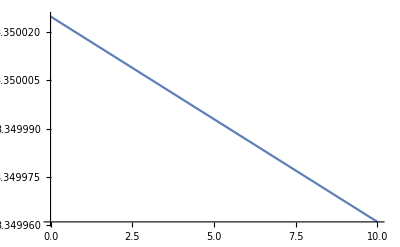

```mathematica
Plot[p[x],{x,0,10}]
```

也可用于非数值特征 - Can also be used on non-numerical features

```mathematica
p=Predict[{-Graphics-->40.2,-Graphics-->8.9,-Graphics-->11,-Graphics-->4.9,-Graphics-->13.6,-Graphics-->15.6,-Graphics-->14.7,-Graphics-->3.8,-Graphics-->34.7,-Graphics-->10.8,-Graphics-->4.,-Graphics-->16.1,-Graphics-->3.3,-Graphics-->8.3,-Graphics-->12.6}]
```

PredictorFunction[…]

```mathematica
p[{-Graphics-,-Graphics-,-Graphics-}]
```

{17.631,13.5,12.0542}

## [A] 文本分类 - Text Classification

使用 Wikipedia 页面中的文本来训练主题分类器 - Use text from Wikipedia pages to train a topic classifier

```mathematica
topics={"Physics","Biology","Mathematics"};
```

```mathematica
texts=WikipediaData/@topics;
```

```mathematica
topicclassifier=Classify[texts->topics]
```

ClassifierFunction[…]

```mathematica
text="";
InputField[Dynamic[text],String,ContinuousAction->True]
Dynamic[Column@topicclassifier[text,"TopProbabilities"->3]]
```

## [A] 图像分类 - Image Classification

根据语义特征对图像进行分类 - Classify images based on their semantic features

```mathematica
classes={"jellyfish","blackberry","octopus","blueberry"};
```

```mathematica
images=WebImageSearch[#,"Thumbnails",MaxItems->30] & /@classes;
```

```mathematica
(*images=Import["images.mx"];*)
```

```mathematica
flatimages =RandomSample[Flatten[images]];
```

低维特征已经合理聚类 - Low-dimensional features are already reasonably clustered

```mathematica
FeatureSpacePlot[flatimages]
```

对图像进行训练，自动提取特征 - Training on images, features are automatically extracted

```mathematica
dataset=Thread/@Thread[images->classes];
```

```mathematica
{trainingset,testset}=TakeDrop[RandomSample[Flatten[dataset]],80];
```

```mathematica
c=Classify[trainingset]
```

测试分类器 - Test the classifier

```mathematica
RandomChoice[testset]
```

```mathematica
c[First[%]]
```

构建一个可以查询的 ClassifierMeasurementsObject  - Build a ClassifierMeasurementsObject that can be queried

```mathematica
cm=ClassifierMeasurements[c,testset];
```

```mathematica
cm["Properties"]//Short
```

```mathematica
cm["Report"]
```

检查错误分类的示例 - Inspect the misclassified examples

```mathematica
cm["WorstClassifiedExamples"->2]
```

```mathematica
c/@%[[All,1]]
```

现在可以通过向黑莓类添加更多植物图像来纠正这种情况 - This could now be corrected by adding more plant images to the blackberry class

## [A] 数据预测 - Data Prediction

http://datarepository.wolframcloud.com

```mathematica
dataset=ResourceData["Sample Data: Boston Homes"];
```

```mathematica
First[dataset]
```

根据其他因素构建房屋价值（”MEDV”列）的预测器 - Build a predictor for the home value (“MEDV” column) based on the other factors

```mathematica
{trainingset,testset}=TakeDrop[RandomSample[dataset],400];
```

```mathematica
p=Predict[trainingset->"MEDV"]
```

PredictorFunction[…]

将预测值与实际值进行比较 - Compare the predictions with the actual values

```mathematica
pm=PredictorMeasurements[p,testset->"MEDV"];
```

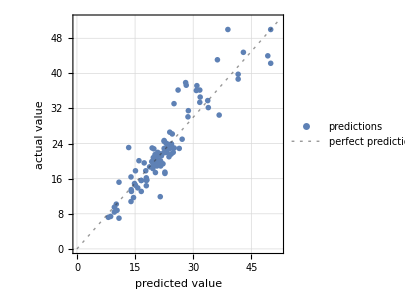

```mathematica
pm["ComparisonPlot"]
```

估计每个特征对特定示例的预测值的影响 - Estimate the impact of each feature on the predicted value for a specific example

```mathematica
p[testset[[1]],"SHAPValues"]
```

<|CRIM→0.326115,ZN→-1.1506,INDUS→0.159054,CHAS→-0.059505,NOX→-0.518392,RM→-1.06578,AGE→1.23243,DIS→-0.59047,RAD→-0.0100801,TAX→0.213151,PTRATIO→-1.16911,BLACK→0.104829,LSTAT→1.7071|>

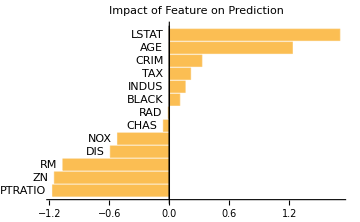

```mathematica
BarChart[Sort[%],]
```

## 监督方法 - Supervised Methods

### 线性回归 - Linear Regression

预测方法 - Method for Predict

参数模型 - Parametric model

prediction(features)=θ_0+θ_1 feature_1+θ_1 feature_2+ ... +θ_n feature_n

P(y|features)∝Exp[-(y-prediction[features])^2/(2 σ^2)]

Minimizes ∑_i (y_i-prediction_i)^2+λ||θ(||)^2 （“L2” 正则化以避免过度拟合） - (“L2” regularization to prevent overfitting)

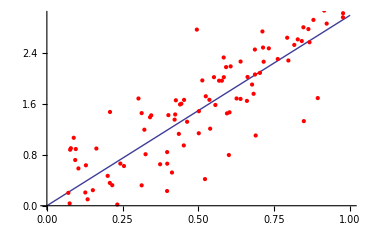
```mathematica
-Graphics-               -Graphics3D-
```

### 逻辑回归 - Logistic Regression

分类方法 - Method for Classify

参数模型 - Parametric model

线性分类器 - Linear classifier

score (class_i|features)∝θ_0^class_i+ θ_1^class_i feature_1+ θ_2^class_i feature_2+ ... + θ_n^class_i feature_n

P(class=class_i|features)=Softmax(score (class_i|features))

Minimizes ∑_i -Log[P(class=class_i|featurevector_i)]+λ/2||θ(||)^2

在神经网络语言中：LinearLayer + SoftmaxLayer

-Graphics3D-

### 最近的邻域 - Nearest Neighbors

分类、预测、学习分布的方法，... - Method for Classify, Predict, LearnDistribution, ...

非参数模型/基于实例的模型 - Non-parametric model / instance-based model

超参数 - Hyperparameter

邻域数 - Number of neighbors

距离函数 - Distance function

-Graphics3D-

### 决策树、随机森林、梯度提升树 - Decision Trees, Random Forest, Gradient-Boosted Trees

分类、预测、学习分布的方法 - Method for Classify, Predict, LearnDistribution

1984 年：分类和回归树 (CART) 算法 - 1984: Classification & regression trees (CART) algorithm

1999 年：梯度增强树（小树序列）- 1999: Gradient-boosted trees (sequence of small trees)

2001年：随机森林（袋装特征的并行处理） - 2001: Random forest (parallel processing on bagged features)

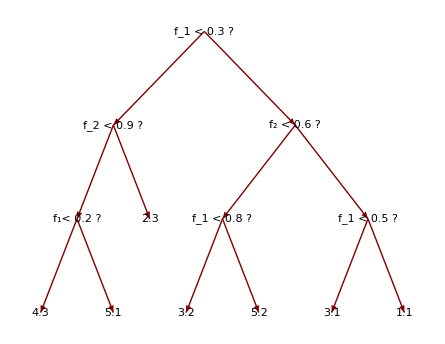
```mathematica
-Graphics--Graphics-
```

### 支持向量机 - Support Vector Machine

分类方法 - Method for Classify

1995

“智能”最近的邻域 - “Smart” nearest neighbors

了解哪些训练示例很重要 - Learn which training examples are important

分配权重 - Assign weights

丢弃远离边界的示例 - Drop examples far from the boundaries

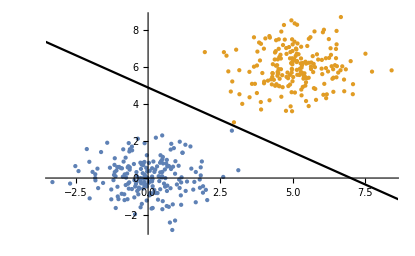

### 高斯过程 - Gaussian Processes

预测方法 - Method for Predict

以数据点为条件的”无限维”多元高斯分布  - “Infinite-dimensional” MultinormalDistribution conditioned by data points

多元高斯分布 - MultinormalDistribution

对新示例使用贝叶斯推断 - Using a Bayesian inference on new examples

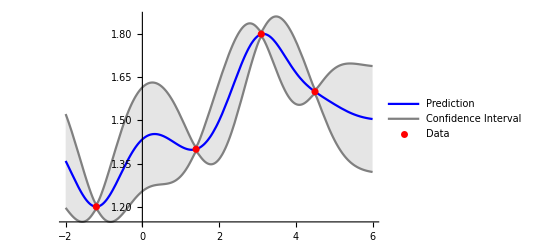

## [P] 分类 - Classification

从 MNIST 数据集创建训练和测试集： - Create a training and test set from the MNIST dataset:

```mathematica
mnist=ResourceData["MNIST"];
```

在”MNIST”数据集上训练分类器 - Train a classifier on the “MNIST” dataset

可视化学习曲线 - Visualize the learning curves

测试其准确性 - Test its accuracy

与训练过程中估计的准确度进行比较 - Compare with the accuracy estimated by the training procedure

可视化混淆矩阵 - Visualize the confusion matrix

从测试集中找到分类最差的例子 - Find the worst-classified example from the test set

分析其预测概率 - Analyze its predicted probabilities

## 聚类 - Clustering

无监督学习 - Unsupervised learning

没有输入/输出的区分 - no input/output split

在数据集中查找聚类 - Find clusters in a dataset

### 基本聚类 - Basic Clustering

根据相似性将数据拆分为聚类 - Splits data into clusters based on similarity

```mathematica
FindClusters[{-10,-9,-8,-7,5,6,7,8}]
```

{{-10,-9,-8,-7},{5,6,7,8}}

给出每个点的聚类 - Give the cluster for each point

```mathematica
ClusteringComponents[{-10,-9,-8,-7,5,6,7,8}]
```

{1,1,1,1,2,2,2,2}

将图像像素聚类为 3D {r,g,b} 或 1D {gray-level}点 - Cluster image pixels as 3D {r,g,b} or 1D {gray-level} points

```mathematica
ClusteringComponents[-Graphics-,5]//Colorize
```

-Graphics-

### ClusterClassify

预测新点的聚类 - Predict clusters for new points

```mathematica
c=ClusterClassify[{-10,-9,-8,-7,5,6,7,8}]
```

ClassifierFunction[…]

```mathematica
c[{-10.3,4}]
```

{2,1}

## [A] 点簇 - Point Clusters

生成和可视化 2D 点为两个聚类- Generate and visualize 2D points in two clusters

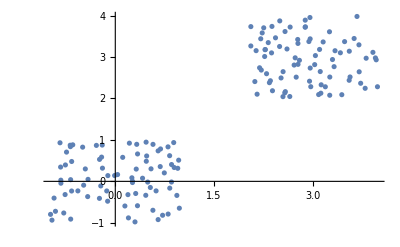

```mathematica
data = Join[RandomReal[{-1, 1}, {80, 2}], RandomReal[{2, 4}, {80, 2}]];
ListPlot[data]
```

在数据集中查找聚类并显示它们 - Find clusters in the dataset and display them

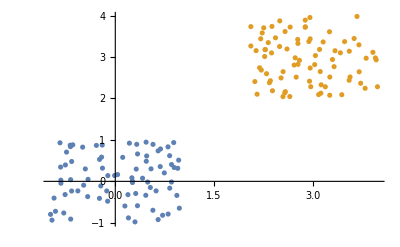

```mathematica
ListPlot[FindClusters[data]]
```

## [A] 图像聚类 - Image Clusters

基于自定义距离的图像聚类 - Cluster images based on a custom distance

```mathematica
faces={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

测量内置名人分类器所估计的概率分布之间的距离 - Measure the distance between the probability distributions estimated by the built-in notable person classifier

```mathematica
proba=Values[Classify["NotablePerson",faces,"Probabilities"]];
```

```mathematica
KLDivergence[proba1_,proba2_] := ((proba1-proba2)/2).(Log[Clip[proba1,{$MachineEpsilon,Infinity}
]]-Log[Clip[proba2,{$MachineEpsilon,Infinity}
]])
```

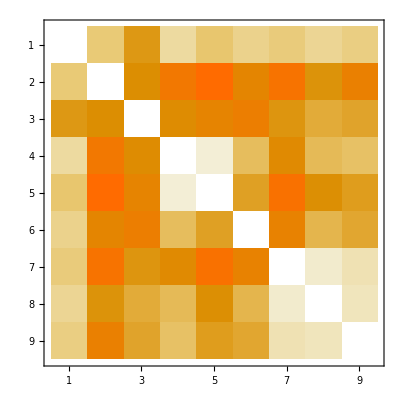

```mathematica
DistanceMatrix[proba,DistanceFunction->KLDivergence]//MatrixPlot
```

根据这个距离找到三个聚类 - Find three clusters based on this distance

```mathematica
FindClusters[proba->faces,3,DistanceFunction->KLDivergence]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

## [A] 色聚类 - Color Clusters

将图像转换为 LAB 颜色空间以获得感知上更精确的距离 - Convert an image to the LAB color space to get more perceptually precise distances

```mathematica
image = ColorConvert[-Graphics-, "LAB"];
```

对图像的像素值数组给出的数据进行聚类 - Cluster the data given by the array of pixel values of the image

```mathematica
imageData = Flatten[ImageData[image], 1];
```

```mathematica
c=ClusterClassify[imageData, 5, Method->"KMedoids"]
```

ClassifierFunction[…]

使用分类器将聚类分配给每个像素 - Use the classifier to assign clusters to each pixel

```mathematica
decision=c[imageData];
```

使用分类器函数找到五种主色 - Use the classifier function to find four dominant colors

```mathematica
colors=LABColor@@@(Mean/@(Pick[imageData, decision, #]&/@Range[5]))
```

{LABColor[0.4523633256250044, -0.016829808029236216, -0.341053138450101],LABColor[0.19271654037253136, 0.08106075538283161, 0.22303782764286292],LABColor[0.3293870171097869, -0.10658767398350691, 0.3253651372295602],LABColor[0.6499851643770013, 0.19301624907986092, 0.6755397185172723],LABColor[0.825370527043161, 0.06095823218107275, 0.7901509545850657]}

使用分类器获取每种主色的二进制掩码 - Use the classifier to get binary masks for each dominant color

```mathematica
components=Image/@ComponentMeasurements[{image,Partition[decision, 426]},"Mask"][[All,2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

重建原始图像的量化版本 - Reconstruct a quantized version of the original image

```mathematica
ImageAdd@@MapThread[ImageMultiply,{components,colors}]
```

-Graphics-

## 聚类方法 - Clustering Methods

### KMeans

FindClusters、ClusterClassify 和  ClusteringComponents 的方法 - Method for FindClusters, ClusterClassify and ClusteringComponents

基于质心的聚类 - Centroid-based clustering

最适用于小型各向同性聚类 - Works best on small, isotropic clusters

-Graphics-

### 生成树 - SpanningTree

FindClusters、ClusterClassify 和 ClusteringComponents 的方法 - Method for FindClusters, ClusterClassify and ClusteringComponents

寻找构成数据点间的最小生成树（使用距离作为图权重) - Finds the minimum spanning tree of data points (using distances as graph weights)

然后修剪树的最长边 - The longest edges of the tree are then pruned

### 基于密度的噪声应用空间聚类 - DBSCAN

FindClusters、ClusterClassify 和 ClusteringComponents 的方法 - Method for FindClusters, ClusterClassify and ClusteringComponents

对核心点、边缘点和噪声中的数据进行分类 - Classify data in core points, edge points and noise

当聚类具有相似密度时效果最佳 - Works best when clusters have similar density

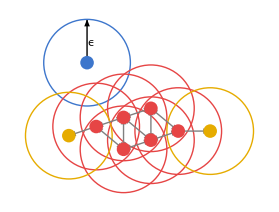

### 玩具示例 - Toy Examples

## [P] 聚类 - Clustering

可视化 Fisher Iris 数据集： - Visualize the Fisher Iris dataset:

```mathematica
iris=ExampleData[{"MachineLearning","FisherIris"},"Data"][[All,1,{1,3}]];
```

聚类和可视化数据 - Cluster and visualize the data

使用聚类方法 - Play with the clustering methods

## 降维 - Dimensionality Reduction

将示例转换为较低维度的数值向量 - Transform examples into numeric vectors of lower dimensions

### 点- Points

创建 3D 点的集合 - Create a collection of 3D points

```mathematica
vectors=Join[RandomReal[{0,3},{1000,3}], RandomReal[{2,5},{1000,3}],RandomReal[{4,7},{1000,3}]];
```

```mathematica
ListPointPlot3D[vectors]
```

-Graphics3D-

训练降维器将它们映射到二维空间 - Train a dimensionality reducer to map them to a 2D space

```mathematica
dr=DimensionReduction[vectors,2]
```

DimensionReducerFunction[…]

```mathematica
dr[{0.3,0.2,0.4}]
```

{3.00717,0.00455445}

绘制简化向量 - Plot the reduced vectors

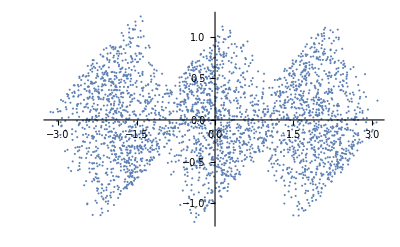

```mathematica
ListPlot[dr[vectors]]
```

将原始 3D 点与低维重建进行比较 - Compare original 3D points with a reconstruction for lower dimension

```mathematica
reconstructed=dr[vectors,"ReconstructedData"];
```

```mathematica
ListPointPlot3D[{vectors,reconstructed}]
```

-Graphics3D-

### 图像 - Images

在低维空间中表示图像 - Represent images in a low-dimensional space

```mathematica
images={-Graphics-,-Graphics-,-Graphics- ,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
points=DimensionReduce[images,2]
```

{{16.6901,0.663866},{8.66664,12.1655},{23.1908,-8.59529},{-14.2674,-21.1948},{-19.8211,-4.7848},{-14.459,21.7455}}

```mathematica
ListPlot[MapThread[Callout,{points,Image[images,ImageSize->40]}]]
```

-Graphics-

## [A] 缺失数据插补 - Missing Data Imputation

从 MNSIT 数据集中获取训练数据 - Get the training data from the MNSIT dataset

```mathematica
digits=RandomSample[ResourceData["MNIST"][[All,1]],10000];
```

```mathematica
RandomSample[digits,10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

使用像素值创建训练集 - Create a training set with the pixel value

```mathematica
digits=Flatten[ImageData[#]]&/@RandomSample[digits];
trainingset=digits[[;;9000]];
testset=digits[[9001;;]];
```

构建一个 DimensionReducerFunction - Build a DimensionReducerFunction

```mathematica
digits[[1]]//Length
```

784

```mathematica
dr= DimensionReduction[trainingset,50]
```

DimensionReducerFunction[…]

通过反转降维重构图像数据 - Reconstruct the image data by inverting the dimensionality reduction

```mathematica
toimage=Image[Partition[#,28], ImageSize->Tiny] &;
```

```mathematica
vector=RandomChoice[testset];
toimage /@ {vector,dr[vector,"ReconstructedVectors"]}
```

{-Graphics-,-Graphics-}

该过程可以处理丢失的数据 - The procedure can work on missing data

```mathematica
vectormissing=vector;
vectormissing[[309;;364]]=Missing[];
imagemissing = toimage[Replace[vectormissing, _Missing-> .5,{1}]]
```

-Graphics-

将原始图像与重建图像进行比较 - Compare the original image with the reconstruction

```mathematica
imputedimage=toimage[dr[vectormissing, "ImputedVectors", PerformanceGoal->"Quality"]];
```

-Graphics- | -Graphics- | -Graphics-
original image | missing data | reconstructed image

## 学习分布 - LearnDistribution

目标：学习数据的概率分布

应用：

生成新示例 - Generating new examples (RandomVariate)

异常检测 - Anomaly detection (AnomalyDetection)

填写缺失值 - Fill-in missing values (SynthesizeMissingValues)

预测任何变量作为其他变量的函数 - Predict any variable as function of others

去噪/纠错 - Denoising/error correction

半监督学习 - Semi-supervised learning

...

### 分类空间 - Categorical Space

```mathematica
ld=LearnDistribution[{"A","A","B","B","B"}]
```

LearnedDistribution[…]

```mathematica
Information[ld]
```

Distribution information
Data type | Nominal
Dimension | 1
Method | ContingencyTable
Loss | 0.769 ± 0.096
Entropy | 0.674 ± 0.0045
PDF query speed | 114. examples/ms
Sampling speed | 40.6 examples/ms
Model memory | 76.5 kB
Training examples used | 5 examples
Training time | 1.94 s

```mathematica
RandomVariate[ld,10]
```

{B,A,B,B,A,B,A,B,A,A}

```mathematica
Tally[RandomVariate[ld,100]]
```

{{B,63},{A,37}}

```mathematica
PDF[ld,{"A","B"}]
```

{0.428571,0.571429}

```mathematica
{2,3}/5.
```

{0.4,0.6}

### 数值空间 - Numeric Space

```mathematica
iris=ExampleData[{"MachineLearning","FisherIris"},"Data"][[All,1,{1,3}]];
```

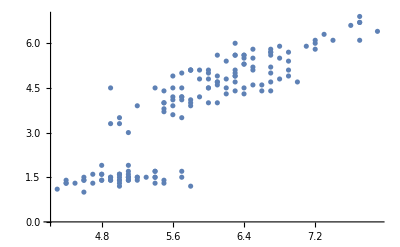

```mathematica
ListPlot[iris]
```

```mathematica
ld=LearnDistribution[iris]
```

LearnedDistribution[…]

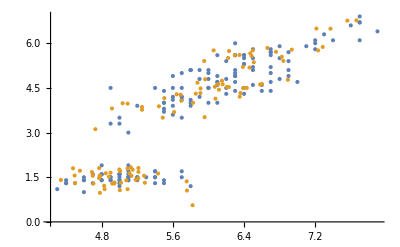

```mathematica
ListPlot[{iris,RandomVariate[ld,100]}]
```

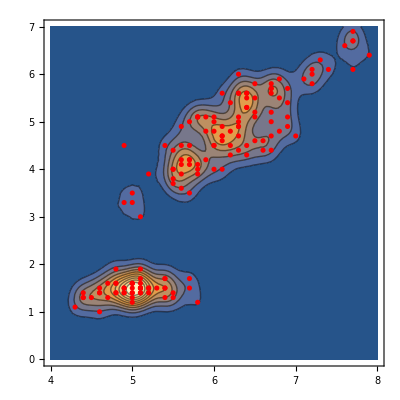

```mathematica
Show[ContourPlot[PDF[ld,{x,y}],{x,4,8},{y,0,7},PlotRange->All,Contours->10],ListPlot[iris, PlotStyle->Red]]
```

```mathematica
SynthesizeMissingValues[ld,{5.5,Missing[]}]
```

{5.5,3.64909}

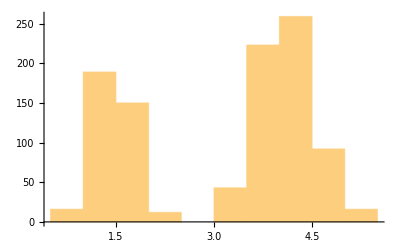

```mathematica
Histogram[Table[Last@SynthesizeMissingValues[ld,{5.5,Missing[]}],1000]]
```

```mathematica
SynthesizeMissingValues[ld,{5.5,Missing[]},Method->"ModeFinding"]
```

{5.5,3.86167}

### 结构化数据 - Structured Data

```mathematica
titanic=ResourceData["Sample Data: Titanic Survival"]
```

Dataset[<>]

```mathematica
ld=LearnDistribution[titanic,TimeGoal->10]
```

LearnedDistribution[…]

```mathematica
Information[ld]
```

Distribution information
Data type | Mixed (number: 4)
Dimension | 4
Method | ContingencyTable
Loss | 10.7 ± 0.1
Entropy | 45.6 ± 2.3
PDF query speed | 27.7 examples/s
Sampling speed | 8.92 examples/ms
Model memory | 184. kB
Training examples used | 1309 examples
Training time | 10.8 s

```mathematica
RandomVariate[ld,10]
```

```mathematica
PDF[ld,<|"Class"->"1st", "Sex"->"female", "Age"->Quantity[20, "Years"],"SurvivalStatus"->"survived"|>]
```

4.87559×10^-11

```mathematica
PDF[ld,<|"Class"->"3rd", "Sex"->"male", "Age"->Quantity[80, "Years"],"SurvivalStatus"->"survived"|>]
```

8.84811×10^-13

```mathematica
PDF[ld,<|"Class"->"3rd", "Sex"->"male", "Age"->Quantity[150, "Years"],"SurvivalStatus"->"survived"|>]
```

1.338146315246×10^-316

```mathematica
SynthesizeMissingValues[ld,<|"Class"->"1st"|>]
```

<|Class→1st,Age→23.1488 yr,Sex→female,SurvivalStatus→died|>

## [P] 学习分布 - LearnDistribution

了解木星卫星数据集的分布(Learn the distribution of the Jupiter moons dataset):

```mathematica
data=Values@ExampleData[{"Dataset","Planets"}]["Jupiter","Moons"]
```

生成随机卫星 - Generate random moons

计算一个假想月亮的 PDF - Compute the PDF of an imaginary moon

从数据集中估算缺失值 - Impute the missing values from the dataset

试玩转插补方法 - Play with the imputation methods

## LearnDistribution 的方法们 - Methods

### 多元正态(高斯)分布 - Multinormal

LearnDistribution 的方法之一 - Method for LearnDistribution

如同 - Similar to

线性回归 - Linear regression

主成分分析 - Principal component analysis (PCA)

```mathematica
ld=LearnDistribution[iris,Method->"Multinormal"]
```

LearnedDistribution[…]

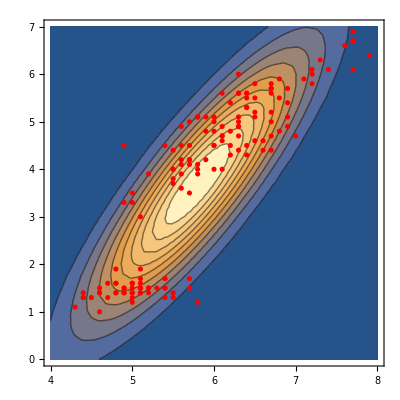

```mathematica
Show[ContourPlot[PDF[ld,{x,y}],{x,4,8},{y,0,7},PlotRange->All,Contours->10],ListPlot[iris, PlotStyle->Red]]
```

### 高斯混合 - GaussianMixture

LearnDistribution 的方法之一 - Method for LearnDistribution

```mathematica
ld=LearnDistribution[iris,Method->"GaussianMixture"]
```

LearnedDistribution[…]

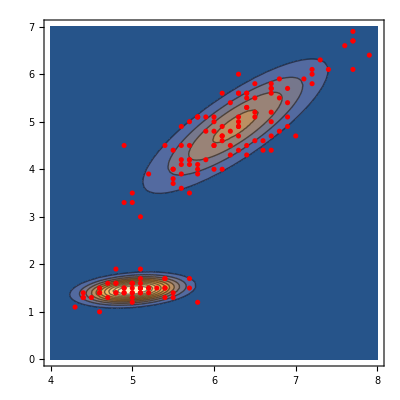

```mathematica
Show[ContourPlot[PDF[ld,{x,y}],{x,4,8},{y,0,7},PlotRange->All,Contours->10],ListPlot[iris,PlotStyle->Red]]
```

### 核密度估计 - KernelDensityEstimation

LearnDistribution 的方法之一 - Method for LearnDistribution

使用简单分布的混合对概率密度建模。
-Models probability density with a mixture of simple distributions

〜最近的邻居 - ~ NearestNeighbors

```mathematica
ld=LearnDistribution[iris,Method->"KernelDensityEstimation"]
```

LearnedDistribution[…]

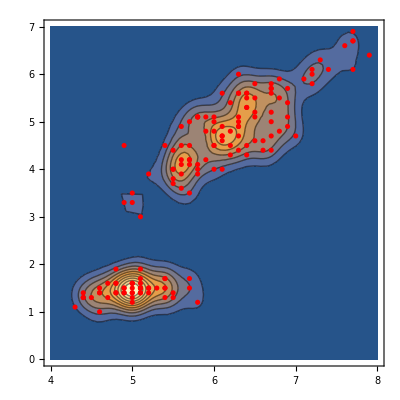

```mathematica
Show[ContourPlot[PDF[ld,{x,y}],{x,4,8},{y,0,7},PlotRange->All,Contours->10],ListPlot[iris,PlotStyle->Red]]
```

### 离散化数据并存储每个可能的概率 - ContingencyTable

LearnDistribution 的方法之一 - Method for LearnDistribution

```mathematica
ld=LearnDistribution[iris,Method->"ContingencyTable"]
```

LearnedDistribution[…]

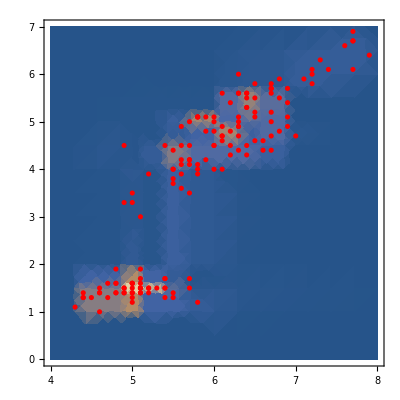

```mathematica
Show[DensityPlot[PDF[ld,{x,y}],{x,4,8},{y,0,7},PlotRange->All],ListPlot[iris, PlotStyle->Red]]
```

## FindDistribution & FindFormula

目标：找到简单的可解释模型（数据挖掘任务) - Goal: find simple interpretable model (data mining task)

### FindDistribution

```mathematica
d = MixtureDistribution[{0.3,0.7},{ExponentialDistribution[1],NormalDistribution[5,0.8]}];
```

```mathematica
samples=RandomVariate[d,1000]
```

```mathematica
Histogram[samples]
```

```mathematica
dist=FindDistribution[samples]
```

```mathematica
Histogram[samples,Automatic,"PDF"]
```

```mathematica
Show[Histogram[samples,Automatic,"PDF"],Plot[PDF[dist,x],{x,0,8}]]
```

### FindFormula

```mathematica
data =Table[{x, Sin[2x]+Cos[x]+RandomReal[{-.2,.2}]}, {x, RandomReal[{0, 10}, 200]}];
```

```mathematica
ListPlot[data]
```

```mathematica
formula=FindFormula[data]
```

```mathematica
Show[Plot[formula[x],{x,0,10}],ListPlot[data]]
```

## 良好做法 - Good Practices

随机选取数据集 (RandomSample) - Shuffle the dataset (RandomSample)

将训练集与测试集分离 - Separate training set from test set

从一个小的训练集开始 - Start with a small training set

Just need a laptop in the beginning

开始使用简单的功能 - Start using simple functions

e.g. Classify or Predict on raw data for a baseline

绘制学习曲线（性能与训练集大小 - Plot a learning curve (performance vs. training set size)

## 如何训练模型？- How to Train a Model?

### Optimization Experiment

### 优化实验

迭代调整参数以更好地执行任务 - Tune parameters iteratively to perform the task better

经常：沿最陡的下降 - Often: steepest descent

根据汽车的速度找到汽车的停车距离 - Find the stopping distance of a car based on its speed

```mathematica
data=RandomSample@ResourceData["Sample Data: Car Stopping Distances"]
```

```mathematica
dataplot=ListPlot[data,Frame->True,PlotMarkers->"OpenMarkers",PlotLegends->{"data"},
PlotRange->{{0,30},{-5,100}},FrameLabel->(Style[#,15]&/@{"Speed (mi/h)","Distance (ft)"})]
```

建立一个简单的线性模型 - Set up a simple linear model

```mathematica
f[a_,b_,speed_]:=a*speed+b;
```

```mathematica
Show[dataplot,Plot[f[1,2,speed],{speed,0,30},PlotLegends->{Style["f[1, 2, speed]","CodeText"]},PlotStyle->Red]]
```

定义成本/损失函数 - Define a cost/loss function

```mathematica
Clear[loss,x,y]
loss[a,b]=="1/m"Sum[(Inactive[f][Subscript[x, i],a,b]-Subscript[y, i])^2,{i,1,m}] //Magnify//TraditionalForm
```

```mathematica
x=Normal[QuantityMagnitude[data[All,"Speed"]]];
y=Normal[QuantityMagnitude[data[All,"Distance"]]];
```

```mathematica
loss[a_,b_]:=Mean[(f[a,b,x]-y)^2]
```

绘制对数损失 - Plot the logarithmic loss

```mathematica
Row[{DensityPlot[Callout[Log[loss[a,b]],],{a,-10,10},{b,-100,100},],Plot3D[Log[loss[a,b]],{a,-10,10},{b,-100,100},]},]
```

找到最小化损失的参数值 - Find the values of the parameters that minimize the loss

```mathematica
{Subscript[a, opt],Subscript[b, opt]}=FindArgMin[loss[a,b],{a,b}]
```

绘制解 - Plot the solution

```mathematica
Show[dataplot,Plot[f[Subscript[a, opt],Subscript[b, opt],speed],{speed,0,30},PlotLegends->{Style["f[a_opt, b_opt, speed]","CodeText"]},PlotStyle->Red]]
```

## To Know More about Machine Learning…

## 要了解有关机器学习的更多信息……

### Resources

### 资源

#### Wolfram 语言 - Wolfram Language

文档 - Documentation

http://reference.wolfram.com/language/ref/Classify.html

机器学习教程 - Machine learning tutorial

https://www.wolfram.com/language/introduction-machine-learning/

深度学习教程 - Deep learning tutorial

https://reference.wolfram.com/language/tutorial/NeuralNetworksOverview.html

完整的机器学习项目示例 - Example of a complete machine learning project

http://blog.wolfram.com/2014/06/20/predicting-who-will-win-the-world-cup-with-wolfram-language

http://blog.wolfram.com/2014/06/26/world-cup-follow-up-update-of-winning-probabilities-and-betting-results

#### 在线视频 - Online Video

Machine Learning, Andrew Ng (Coursera)

MachineLearning, Littman & Isbell (Udacity)

Fast.ai lectures

Probabilistic Graphical Models, Daphne Koller (Coursera)

Machine Learning summer school (VideoLectures.NET)

#### 图书 - Books

Machine Learning: a Probabilistic Perspective (Murphy, 2012). Webpage. Introduction.

Deep Learning (Ian Goodfellow, Yoshua Bengio and Aaron Courville, 2016)

Pattern Recognition and Machine Learning (Bishop, 2006). Webpage

The Elements of Statistical Learning (Hastie, Tibshirani, Friedman, 2001). Last version.

Information Theory, Inference and Learning Algorithms (MacKay, 2003)

Introduction to Machine Learning (Smola, Vishwanathan, 2008).

### 教育 Education

目前,多学科领域 -  Currently, multi-disciplinary field

计算机科学 - Computer Science

统计数据 - Statistics

物理 - Physics

应用数学 - Applied Mathematics

工程 - Engineering